# Tools for Complex

## Plots

```mathematica
ComplexPlot3D[Exp[z],{z,π},PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
f[z_]:= Sin[z^2]/((1+z^2)^2)
g[z_]:= √(1+z^2)
ComplexPlot3D[f[z],{z,2},PlotLegends->Automatic]
ComplexPlot3D[g[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

-Graphics3D-

```mathematica
h[z_]:=√(z+ⅈ)
ComplexPlot3D[h[z],{z,2},PlotLegends->Automatic]
```

-Graphics3D-

## Parameterizations

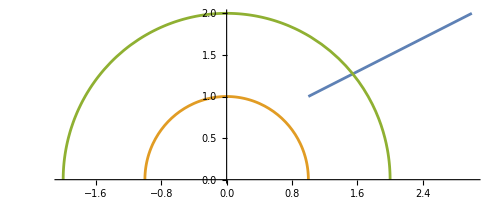

```mathematica
Clear[z1,z2,t,a,b]
z1[t_]:= 1+ⅈ + t (2 +ⅈ)
z2[t_]:= ⅇ^(π  ⅈ t)
z3[t_]:= 2 ⅇ^(π  ⅈ t^2)
ParametricPlot[{
ReIm[z1[t]],
ReIm[z2[t]],
ReIm[z3[t]]},{t,0, 1}]
```

## Mappings

### f(z)=z^2

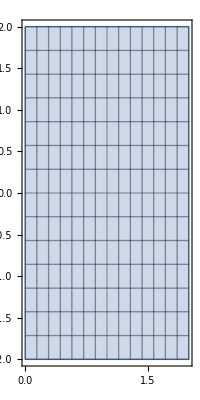
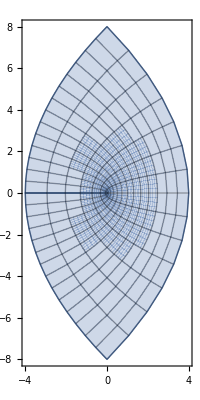
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^2
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

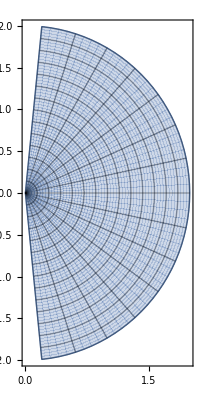
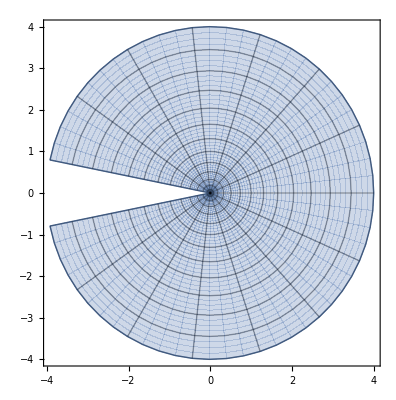
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2+0.1,π/2-0.1},
Mesh->Full,
PlotRange->All]}
```

### f(z)=z^(1/2)

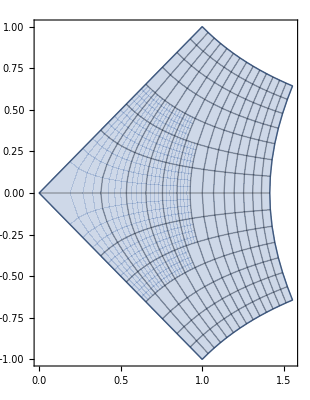
{-Graphics-,⟶,-Graphics-}

```mathematica
f[z_]:= z^(1/2)
{ParametricPlot[ReIm[x+ I y],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[x+ I y]],{x,0,2},{y,-2,2},
Mesh->Full,
PlotRange->All]}
```

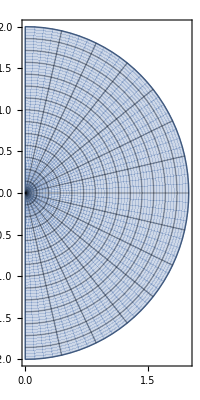
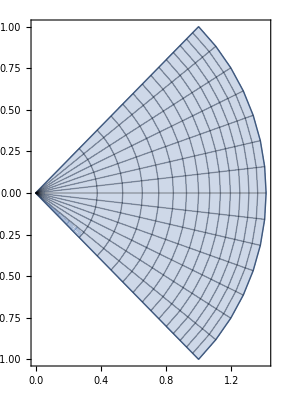
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
PlotRange->All]}
```

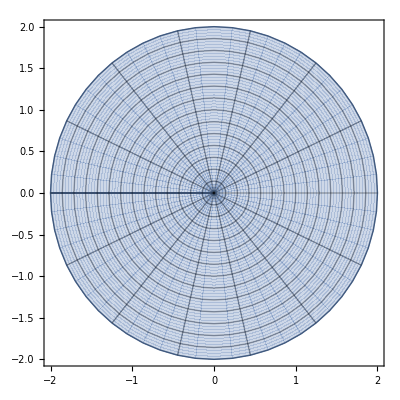
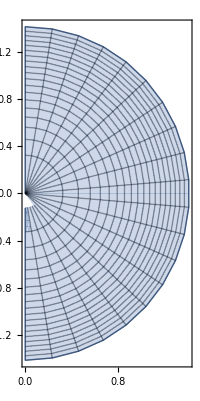
{-Graphics-,⟶,-Graphics-}

```mathematica
{ParametricPlot[ReIm[r ⅇ^(ⅈ θ)],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotRange->All],"⟶",
ParametricPlot[ReIm[f[r ⅇ^(ⅈ θ)]],{r,0,2},{θ,-π,π},
Mesh->Full,
PlotPoints->20,
PlotRange->All]}
```

### f(z)=a+ b z

0.0707107+0.0707107 ⅈ

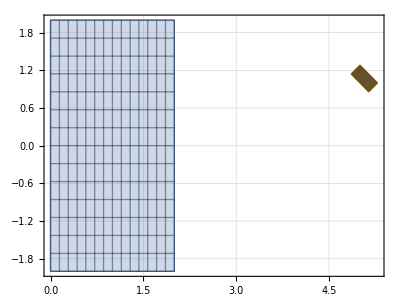

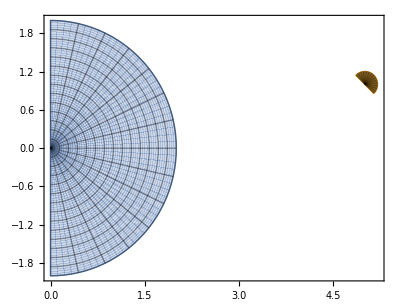

```mathematica
θ=π/4;
a=0.1 ⅇ^(ⅈ θ)
b=5+ⅈ;
f[z_]:=a z + b 
ParametricPlot[{ReIm[x+ I y],ReIm[f[x+ I y]]},{x,0,2},{y,-2,2},
Mesh->Full,
GridLines->Automatic,
AspectRatio->Automatic,
PlotRange->All]
ParametricPlot[{ReIm[r E^(I θ)],ReIm[f[r E^(I θ)]]},{r,0,2},{θ,-π/2,π/2},
Mesh->Full,
AspectRatio->Automatic,
PlotRange->All]
```